```mathematica
1+1
```

2

```mathematica
tape={};
```

```mathematica
Head[Plus]
```

Symbol

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
D[expr[x1, x2],{{x1, x2}}]
```

{expr^(1,0)[x1,x2],expr^(0,1)[x1,x2]}

```mathematica
Keys[<|a->1, b->2|>]
```

{a,b}

```mathematica
ClearAll[ad]
ad /: f[ad[expr_,  y_]]:=Module[{out=f[expr],jac}, jac=Derivative[1][f][expr];ad[out, jac y]]
ad/:f[ad[expr1_, y1_], ad[expr2_, y2_]] := Module[{out=f[expr1, expr2], jac}, jac={Derivative[1,0][f][expr1, expr2], Derivative[0, 1][f][expr1, expr2]}; ad[out, Dot[jac, {y1, y2}]]]
```

```mathematica
f[ad[Sin[x1^2 + x2] x3+x3^3, σ]]
```

ad[f[x3^3+x3 Sin[x1^2+x2]],σ f'[x3^3+x3 Sin[x1^2+x2]]]

```mathematica
f[ad[Exp[x1 +x2^3], σ1], ad[Sin[x3^2+Log[x1]], σ2]]
```

ad[f[ⅇ^(x1+x2^3),Sin[x3^2+Log[x1]]],σ2 f^(0,1)[ⅇ^(x1+x2^3),Sin[x3^2+Log[x1]]]+σ1 f^(1,0)[ⅇ^(x1+x2^3),Sin[x3^2+Log[x1]]]]

## Quick check

```mathematica
x=ad[{x1, x2, x3, x4},  DiagonalMatrix[{Subscript[σ, 1], Subscript[σ, 2], Subscript[σ, 3], Subscript[σ, 4]}]]
```

ad[{x1,x2,x3,x4},{{σ_1,0,0,0},{0,σ_2,0,0},{0,0,σ_3,0},{0,0,0,σ_4}}]

```mathematica
tape=Association[1-> x[[2]]]
```

<|1→{{σ_1,0,0,0},{0,σ_2,0,0},{0,0,σ_3,0},{0,0,0,σ_4}}|>

```mathematica
ufun[z_]:={f[z[[1]], z[[2]], z[[4]]], g[z[[2]], z[[4]]], h[z[[4]]]}
```

```mathematica
(*u=With[{out=ufun[x[[1]]]},
ad[out, D[out, {x[[1]]}]]
]*)
```

```mathematica
u=Module[{out=ufun[x[[1]]], jac},
jac=D[out, {x[[1]]}];
AppendTo[tape, (Max[Keys[tape]]+1)->jac];
ad[out, jac]
]
```

ad[{f[x1,x2,x4],g[x2,x4],h[x4]},{{f^(1,0,0)[x1,x2,x4],f^(0,1,0)[x1,x2,x4],0,f^(0,0,1)[x1,x2,x4]},{0,g^(1,0)[x2,x4],0,g^(0,1)[x2,x4]},{0,0,0,h'[x4]}}]

```mathematica
vfun[z_]:={w1 z[[1]]^2+ w2 z[[2]] + w3 z[[3]]}
```

```mathematica
(*v=With[{out=vfun[u[[1]]]},
ad[out, D[out, {u[[1]]}]]
]*)
```

```mathematica
v=Module[{out=vfun[u[[1]]], jac},
jac=D[out, {u[[1]]}];
AppendTo[tape, (Max[Keys[tape]]+1)->jac];
ad[out, jac]
]
```

ad[{w1 f[x1,x2,x4]^2+w2 g[x2,x4]+w3 h[x4]},{{2 w1 f[x1,x2,x4],w2,w3}}]

```mathematica
tape
```

<|1→{{σ_1,0,0,0},{0,σ_2,0,0},{0,0,σ_3,0},{0,0,0,σ_4}},2→{{f^(1,0,0)[x1,x2,x4],f^(0,1,0)[x1,x2,x4],0,f^(0,0,1)[x1,x2,x4]},{0,g^(1,0)[x2,x4],0,g^(0,1)[x2,x4]},{0,0,0,h'[x4]}},3→{{2 w1 f[x1,x2,x4],w2,w3}}|>

```mathematica
Dot@@Values[tape[[ReverseSort[Keys[tape]]]]]
```

{{2 w1 f[x1,x2,x4] σ_1 f^(1,0,0)[x1,x2,x4],σ_2 (w2 g^(1,0)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,1,0)[x1,x2,x4]),0,σ_4 (w3 h'[x4]+w2 g^(0,1)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,0,1)[x1,x2,x4])}}

```mathematica
Dot @@(Transpose /@ Values[tape[[Sort[Keys[tape]]]]])
```

{{2 w1 f[x1,x2,x4] σ_1 f^(1,0,0)[x1,x2,x4]},{w2 σ_2 g^(1,0)[x2,x4]+2 w1 f[x1,x2,x4] σ_2 f^(0,1,0)[x1,x2,x4]},{0},{w3 σ_4 h'[x4]+w2 σ_4 g^(0,1)[x2,x4]+2 w1 f[x1,x2,x4] σ_4 f^(0,0,1)[x1,x2,x4]}}

```mathematica
Dot[v[[2]],u[[2]], x[[2]]]
```

{2 w1 f[x1,x2,x4] σ_1 f^(1,0,0)[x1,x2,x4],σ_2 (w2 g^(1,0)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,1,0)[x1,x2,x4]),0,σ_4 (w3 h'[x4]+w2 g^(0,1)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,0,1)[x1,x2,x4])}

```mathematica
Dot[Transpose[u[[2]]], Transpose[{v[[2]]}], {Subscript[σ, y]}]
```

{2 w1 f[x1,x2,x4] σ_y f^(1,0,0)[x1,x2,x4],σ_y (w2 g^(1,0)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,1,0)[x1,x2,x4]),0,σ_y (w3 h'[x4]+w2 g^(0,1)[x2,x4]+2 w1 f[x1,x2,x4] f^(0,0,1)[x1,x2,x4])}

## Work with the tape

### Example 1

```mathematica
$tape=<|0->Nothing|>
```

<|0→Nothing|>

```mathematica
ClearAll[ad]
```

```mathematica
ad /: ad[expr1_]+ad[expr2_]:=Module[{out, jac},
out=expr1+expr2;
jac={{1, 1}};
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]

ad /: ad[expr1_] ad[expr2_]:=Module[{out, jac},
out=expr1 expr2;
jac={{expr2, expr1}};
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]

ad/:f_[ad[expr_]]:=Module[{out, jac},
out=f[expr];
jac=D[out, {expr}];
jac=If[ArrayDepth[jac]==1, {jac}, jac];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]
```

```mathematica
$tape
xVar=Identity[ad[{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]}]];
$tape
```

<|0→Nothing|>

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}|>

```mathematica
u=ad[xVar[[1]]]+ad[xVar[[2]]]+ad[xVar[[4]]]
$tape
```

Part::partw: Part 2 of ad[{x_1,x_2,x_3,x_4}] does not exist.

Part::partw: Part 4 of ad[{x_1,x_2,x_3,x_4}] does not exist.

ad[{ad[{x_1,x_2,x_3,x_4}]⟦2⟧+ad[{x_1,x_2,x_3,x_4}]⟦4⟧+x_1,ad[{x_1,x_2,x_3,x_4}]⟦2⟧+ad[{x_1,x_2,x_3,x_4}]⟦4⟧+x_2,ad[{x_1,x_2,x_3,x_4}]⟦2⟧+ad[{x_1,x_2,x_3,x_4}]⟦4⟧+x_3,ad[{x_1,x_2,x_3,x_4}]⟦2⟧+ad[{x_1,x_2,x_3,x_4}]⟦4⟧+x_4}]

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},3→{Short^(1,0)[{x_1,x_2,x_3,x_4},5] Shallow^(1,{0,0})[{x_1,x_2,x_3,x_4},{10,50}]},4→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},5→0,6→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},7→0,8→0,9→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},10→{Short^(1,0)[{x_1,x_2,x_3,x_4},5] Shallow^(1,{0,0})[{x_1,x_2,x_3,x_4},{10,50}]},11→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},12→0,13→{{HoldForm^({1,0,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,1,0,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,1,0})[{x_1,x_2,x_3,x_4}],HoldForm^({0,0,0,1})[{x_1,x_2,x_3,x_4}]}},14→0,15→0,16→{{1,1}},17→{{1,1}}|>

```mathematica
u=Sin[ad[xVar]]
$tape
```

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}|>

{Sin[x_1],Sin[x_2],Sin[x_3],Sin[x_4]}

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}}|>

```mathematica
v=Total[ad[u]]
$tape
```

Sin[x_1]+Sin[x_2]+Sin[x_3]+Sin[x_4]

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}},3→{{1,1,1,1}}|>

```mathematica
$tape
```

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}},3→{{1,1,1,1}}|>

```mathematica
Dot@@Values[$tape[[Key /@ ReverseSort[DeleteCases[Keys[$tape], 0]]]]]
```

{{Cos[x_1],Cos[x_2],Cos[x_3],Cos[x_4]}}

```mathematica
Dot@@(Transpose /@ Join[Values[$tape[[Key /@ Sort[DeleteCases[Keys[$tape], 0]]]]], {{{Subscript[σ, y]}}}])
```

{{Cos[x_1] σ_y},{Cos[x_2] σ_y},{Cos[x_3] σ_y},{Cos[x_4] σ_y}}

```mathematica
Dot@@(Transpose /@  Values[$tape[[Key /@ Sort[DeleteCases[Keys[$tape], 0]]]]])
```

{{Cos[x_1]},{Cos[x_2]},{Cos[x_3]},{Cos[x_4]}}

### Example 2

```mathematica
$tape=<|0->Nothing|>
```

<|0→Nothing|>

```mathematica
ClearAll[ad]
```

```mathematica
(*ad /: Total[ad[expr_, vars_]]:=Module[{out, jac},
out=Plus@@expr;
jac=D[out, {vars}];
jac=If[ArrayDepth[jac]==1, {jac}, jac];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]

ad /: Times[ad[expr_, vars_]]:=Module[{out, jac},
out=Times@@expr;
jac=D[out, {vars}];
jac=If[ArrayDepth[jac]==1, {jac}, jac];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]*)

ad /: ad[expr1_, vars1_] + ad[expr2_, vars2_]:=Module[{out, jac},
out=expr1 + expr2;
jac=D[out, ]
]

ad/:f_[ad[expr_, vars_]]:=Module[{out, jac},
out=f[expr];
jac=D[out, {vars}];
jac=If[ArrayDepth[jac]==1, {jac}, jac];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]
```

```mathematica
xVar=Identity[ad[{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]}, {Subscript[x, 1], Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]}]];
$tape
```

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}|>

```mathematica
Times[ad[{xVar[[2]], xVar[[4]]}, {xVar[[2]], xVar[[4]]}]]
```

ad[{x_2,x_4},{x_2,x_4}]

```mathematica
u={Total[ad[{xVar[[1]], xVar[[3]]}, {xVar[[1]],xVar[[3]]}]], Times[ad[{xVar[[2]], xVar[[4]]}, {xVar[[2]], xVar[[4]]}]]}
$tape
```

{x_1+x_3,ad[{x_2,x_4},{x_2,x_4}]}

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{1,1}}|>

```mathematica
v={Sin[ad[u[[1]]]], 2 Cos[ad[u[[2]]]]}
$tape
```

General::ivar: x_1+x_3 is not a valid variable.

General::ivar: x_2 x_4 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{Sin[x_1+x_3],2 Cos[x_2 x_4]}

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{∂_{x_1+x_3} ad[x_1+x_3]},3→{∂_{x_1+x_3} Sin[x_1+x_3]},4→{∂_{x_2 x_4} ad[x_2 x_4]},5→{∂_{x_2 x_4} Cos[x_2 x_4]}|>

### Example 3

```mathematica
$tape=<|0->Nothing|>
```

<|0→Nothing|>

```mathematica
ClearAll[ad]
```

```mathematica
(*ad/: Total[ad[expr_]]:=Module[{out, jac},
out=Plus@@expr;
jac=D[{out}, {expr}];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]

ad /: ad[expr1_] ad[expr2_]:=Module[{out, jac},
out=expr1 expr2;
jac={{expr2, expr1}};
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]
*)
ad/:f_[ad[expr_]]:=Module[{out, jac},
out=f[expr];
jac=D[out, {expr}];
jac=If[ArrayDepth[jac]==1, {jac}, jac];
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]
```

```mathematica
$tape
xVar=ad[{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]}]
$tape
```

<|0→Nothing|>

ad[{x_1,x_2,x_3,x_4}]

<|0→Nothing|>

```mathematica
u=Total[ad[{xVar[[1, 1]], xVar[[1, 2]], xVar[[1, 4]]}]]
$tape
```

ad[x_1+x_2+x_4]

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{1,1,1}}|>

```mathematica
Dot@@Values[$tape[[Key /@ ReverseSort[DeleteCases[Keys[$tape], 0]]]]]
```

Dot::dotsh: Tensors {{1,1,1}} and {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}} have incompatible shapes.

{{1,1,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
u={f[]}
$tape
```

ad[{ad[x_1+x_2+x_4],ad[x_3]}]

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{1,1,1}},3→1,4→{{1,0},{0,1}}|>

```mathematica
u=Sin[ad[xVar]]
$tape
```

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}|>

{Sin[x_1],Sin[x_2],Sin[x_3],Sin[x_4]}

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}}|>

```mathematica
v=Total[ad[u]]
$tape
```

Sin[x_1]+Sin[x_2]+Sin[x_3]+Sin[x_4]

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}},3→{{1,1,1,1}}|>

```mathematica
$tape
```

<|0→Nothing,1→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},2→{{Cos[x_1],0,0,0},{0,Cos[x_2],0,0},{0,0,Cos[x_3],0},{0,0,0,Cos[x_4]}},3→{{1,1,1,1}}|>

```mathematica
Dot@@Values[$tape[[Key /@ ReverseSort[DeleteCases[Keys[$tape], 0]]]]]
```

{{Cos[x_1],Cos[x_2],Cos[x_3],Cos[x_4]}}

```mathematica
Dot@@(Transpose /@ Join[Values[$tape[[Key /@ Sort[DeleteCases[Keys[$tape], 0]]]]], {{{Subscript[σ, y]}}}])
```

{{Cos[x_1] σ_y},{Cos[x_2] σ_y},{Cos[x_3] σ_y},{Cos[x_4] σ_y}}

```mathematica
Dot@@(Transpose /@  Values[$tape[[Key /@ Sort[DeleteCases[Keys[$tape], 0]]]]])
```

{{Cos[x_1]},{Cos[x_2]},{Cos[x_3]},{Cos[x_4]}}

### Example 4

Only ad[] quantities require propagation of sensitivities.
Problem: how to keep track of the variables used in an expression, for instance x_1+x_2+x_4 ?

```mathematica
$test=<|0->Nothing|>
```

<|0→Nothing|>

```mathematica
ClearAll[ad]
```

```mathematica
ad/: {ad[expr_]}:=ad[{expr}]

ad/: ad[expr1_]+ad[expr2_]:=Module[{out, jac},
out=expr1+expr2;
jac={{1, 1}};
AppendTo[$tape, (Max[Keys[$tape]]+1)->jac];
out
]
```

```mathematica
$tape
```

<|0→Nothing,1→{{1,1}}|>

```mathematica
xVar=ad/@{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]}
$tape
```

{ad[x_1],ad[x_2],ad[x_3],ad[x_4]}

<|0→Nothing,1→{{1,1}}|>

```mathematica
ad[xVar[[1]]+xVar[[2]]]+xVar[[4]]
$tape
```

x_1+x_2+x_4

<|0→Nothing,1→{{1,1}},2→{{1,1}},3→{{1,1}}|>

## Setup large test

```mathematica
nVar=4;
vars= StringJoin["var", #] & /@  (ToString /@ Range[nVar]);
vars=Symbol  /@ vars;
nOper=5;
```

```mathematica
args=With[{local:=RandomChoice[Range[nVar]]},
RandomChoice[vars, local] & /@ Range[nOper]
]
```

{{var3,var4},{var4,var4,var3},{var1,var3,var1,var1},{var1},{var1,var3}}

```mathematica
aggregateArgs=Join[Table[Identity, 3], Table[Function[x, Plus @@ x], 1], Table[Function[x, Times @@ x], 1]];
```

```mathematica
poolOfFuncs=Join[{Sin, Cos, Tan, Sinh, Cosh, Tanh,Power[#, -1]&, Power[#, 2]&, Power[#, 3]&, Power[#, 4]&, Exp, Log}, Table[Identity, 1], Table[Function[x, Plus @@ x], 1], Table[Function[x, Times @@ x], 1]];
```

```mathematica
args
```

{{var3,var4},{var4,var4,var3},{var1,var3,var1,var1},{var1},{var1,var3}}

```mathematica
Module[{local=#, aA, aggArg, calc},
aA=RandomChoice[aggregateArgs];
aggArg= aA[local];
aggArg= If[VectorQ[aggArg], aggArg,{aggArg}];
calc=MapThread[#2[#1]&, {aggArg, RandomChoice[poolOfFuncs, Dimensions[{aggArg}][[-1]]]}];
aA=RandomChoice[aggregateArgs];
aggArg= aA[calc];
If[VectorQ[aggArg], aggArg, {aggArg}]
] & /@ args
```

{{1/(var3+var4)},{var3^2 var4^4},{ⅇ^(2 var1) Sin[var1] Sin[var3]},{Sinh[var1]},{Sinh[var1 var3]}}

```mathematica
makeArgs::usage="Builds a random list of `no` arguments by drawing samples of maximum size `nv` from the set `pool`";
makeArgs[pool_, nv_, no_]:=With[{local:=RandomChoice[Range[nv]]},
RandomChoice[pool, local] & /@ Range[no]
]
```

```mathematica
makeArgs[vars, 4, 5]
```

{{var4,var4},{var4,var2,var2,var3},{var4,var3,var4},{var2,var1,var4,var3},{var2,var1,var3,var4}}

```mathematica
makeCalc::usage="Builds a random expression after aggregating the input arguments by sum, product and then applying a random sequence of elementary functions.";
makeCalc[args_]:=
Map[Module[{local},
local=RandomChoice[aggregateArgs][#];
local=If[VectorQ[local], local, {local}];
local=MapThread[#2[#1]&, {local, RandomChoice[poolOfFuncs, Dimensions[{local}][[-1]]]}];
local=RandomChoice[aggregateArgs][local];
If[VectorQ[local], local, {local}]
] &, args]
```

```mathematica
makeCalc[makeArgs[vars, 4, 5]]
```

{{var3^4,var1^2,Tanh[var3],Tanh[var3]},{Sin[var3],ⅇ^var1,Tanh[var3]},{var3 Cosh[var4]},{Log[var1 var2 var4]},{Cos[var2]}}

```mathematica
NestList[makeCalc,makeArgs[vars, 4, 5], 2]
```

{{{var4},{var2,var3,var2,var3},{var3,var2,var1},{var1},{var4,var4,var2}},{{var4^4},{var2^3,Sinh[var3],Cosh[var2],Tan[var3]},{var2^4+var3^4+Sin[var1]},{Sinh[var1]},{var2^2 var4^4}},{{Tanh[var4^4]},{var2^3+Cosh[var2]+Sinh[var3]+Tan[var3]},{var2^4 var3^4 Sin[var1]},{Csch[var1]},{var2^2+var4^4}}}

## Work with the tree

```mathematica
$vertexCount=0;
$tape=<||>;
$graph=Graph[{"x1", "x2", "x3", "x4"}, {},VertexLabels->Automatic];
```

```mathematica
ClearAll[ad]
```

```mathematica
ad/: f_[ad[parentVertex_, expr_]]:=Module[{out, jac, childVertex},
out=f[expr];
jac=D[out, {expr}];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[parentVertex->childVertex]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]
```

```mathematica
xVar={x1, x2, x3, x4}
```

{x1,x2,x3,x4}

```mathematica
u=ufun[ad[{"x1", "x2"},  {x1, x2}]]
```

ad[v1,ufun[{x1,x2}]]

```mathematica
w=wfun[ad[{"x2", "x4"}, {x2, x4}]]
```

ad[v2,wfun[{x2,x4}]]

```mathematica
v=vfun[u]
```

ad[v3,vfun[ufun[{x1,x2}]]]

```mathematica
z=zfun[v]
```

ad[v4,zfun[vfun[ufun[{x1,x2}]]]]

```mathematica
y=yfun[ad[{w[[1]], "x3", "x4"}, {w[[2]], x3, x4}]]
```

ad[v5,yfun[{wfun[{x2,x4}],x3,x4}]]

```mathematica
t=tfun[y]
```

ad[v6,tfun[yfun[{wfun[{x2,x4}],x3,x4}]]]

```mathematica
FindPath[$graph,"x2", t[[1]]]
```

{{x2,v2,v5,v6}}

```mathematica
First[FindPath[$graph, "x2", t[[1]]]] //FullForm
```

List["x2","v2","v5","v6"]

```mathematica
Values[$tape[[Drop[Reverse[First[FindPath[$graph, "x2", t[[1]]]] ], -1]]]]//TableForm
```

tfun'[yfun[{wfun[{x2,x4}],x3,x4}]] |  | 
yfun^({1,0,0})[{wfun[{x2,x4}],x3,x4}] | yfun^({0,1,0})[{wfun[{x2,x4}],x3,x4}] | yfun^({0,0,1})[{wfun[{x2,x4}],x3,x4}]
wfun^({1,0})[{x2,x4}] | wfun^({0,1})[{x2,x4}] |

```mathematica
Dot[{tfun'[yfun[{wfun[{x2,x4}],x3,x4}]]}, {{Derivative[{1,0,0}][yfun][{wfun[{x2,x4}],x3,x4}],Derivative[{0,1,0}][yfun][{wfun[{x2,x4}],x3,x4}],Derivative[{0,0,1}][yfun][{wfun[{x2,x4}],x3,x4}]}}]
```

{tfun'[yfun[{wfun[{x2,x4}],x3,x4}]] yfun^({1,0,0})[{wfun[{x2,x4}],x3,x4}],tfun'[yfun[{wfun[{x2,x4}],x3,x4}]] yfun^({0,1,0})[{wfun[{x2,x4}],x3,x4}],tfun'[yfun[{wfun[{x2,x4}],x3,x4}]] yfun^({0,0,1})[{wfun[{x2,x4}],x3,x4}]}

```mathematica
FindPath[$graph, "x4", t[[1]], Infinity, All]
```

{{x4,v5,v6},{x4,v2,v5,v6}}

```mathematica
FindPath[$graph, "x2", z[[1]], Infinity, All]
```

{{x2,v1,v3,v4}}

```mathematica
Values[$tape[[Drop[Reverse[First[FindPath[$graph, "x2", z[[1]]]] ], -1]]]] // TableForm
```

zfun'[vfun[ufun[{x1,x2}]]] | 
vfun'[ufun[{x1,x2}]] | 
ufun^({1,0})[{x1,x2}] | ufun^({0,1})[{x1,x2}]

## Work with the tree - inverse

```mathematica
$vertexCount=0;
$tape=<||>;
$graph=Graph[{"x1", "x2", "x3", "x4"}, {},VertexLabels->Automatic];
```

```mathematica
ClearAll[ad, adList]
```

```mathematica
ad /: f_[ad[parentVertex_, expr_]]:=Module[{out, jac, childVertex},
out=f[expr];
jac=Association[parentVertex->Derivative[1][out][ expr]];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[childVertex->parentVertex]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]

(* /; ArrayQ[adList, 1, Head[#]==ad &] *)
adList /: f_[adList[adlist_]] := Module[{ args,out, jac, childVertex},
args = Sequence@@adlist[[All, 2]];
out=f[args];
jac=Apply[Association,  Thread[adlist[[All, 1]]->(Derivative[Sequence @@ #][f][args] & /@ IdentityMatrix[Length[adlist]])]];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[childVertex->adlist[[All, 1]]]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]
```

```mathematica
f[ad[1, Pi]]
```

ad[v1,f[π]]

```mathematica
g[adList[{ad[1, Pi], ad[2, ⅇ]}]]
```

ad[v1,g[π,ⅇ]]

```mathematica
(*ad/: f_[ad[parentVertex_, expr_]]:=Module[{out, jac, childVertex},
out=f[expr];
jac=Association[parentVertex->Derivative[1][out][ expr]];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[childVertex->parentVertex]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]
ad/: f_[ad[parentVertex1_, expr1_], ad[parentVertex2_, expr2_]]:=Module[{out, jac, childVertex},
out=f[expr1, expr2];
jac=Association[parentVertex1->Derivative[1,0][out][expr1, expr2], parentVertex2->Derivative[0, 1][out][expr1, expr2]];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[childVertex->{parentVertex1, parentVertex2}]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]
ad/: f_[ad[parentVertex1_, expr1_], ad[parentVertex2_, expr2_], ad[parentVertex3_, expr3_]]:=Module[{out, jac, childVertex},
out=f[expr1, expr2, expr3];
jac=Association[parentVertex1->Derivative[1,0,0][out][expr1, expr2, expr3], parentVertex2->Derivative[0,1,0][out][expr1, expr2, expr3], parentVertex3->Derivative[0,0,1][out][expr1, expr2, expr3]];
$vertexCount++;
childVertex="v"<>ToString[$vertexCount];
$graph= EdgeAdd[$graph, Thread[childVertex->{parentVertex1, parentVertex2, parentVertex3}]];
AssociateTo[$tape, childVertex->jac];
ad[childVertex, out]
]*)
```

```mathematica
x1Var=ad["x1", x1];
x2Var=ad["x2", x2];
x3Var=ad["x3", x3];
x4Var=ad["x4", x4];
```

```mathematica
xVar = {x1Var, x2Var, x3Var, x4Var};
```

```mathematica
(*u=ufun[x1Var, x2Var]*)
u=ufun[adList[{x1Var, x2Var}]]
```

ad[v1,ufun[x1,x2]]

```mathematica
(*w=wfun[x2Var, x4Var]*)
w=wfun[adList[{x2Var, x4Var}]]
```

ad[v2,wfun[x2,x4]]

```mathematica
v=vfun[u]
```

ad[v3,vfun[ufun[x1,x2]]]

```mathematica
z=zfun[v]
```

ad[v4,zfun[vfun[ufun[x1,x2]]]]

```mathematica
(*y=yfun[w, x3Var, x4Var]*)
y=yfun[adList[{w, x3Var, x4Var}]]
```

ad[v5,yfun[wfun[x2,x4],x3,x4]]

```mathematica
t=tfun[y]
```

ad[v6,tfun[yfun[wfun[x2,x4],x3,x4]]]

```mathematica
FindPath[$graph, z[[1]], "x1", Infinity, All]
```

{{v4,v3,v1,x1}}

```mathematica
FindPath[$graph, t[[1]], "x4", Infinity, All]
```

{{v6,v5,x4},{v6,v5,v2,x4}}

```mathematica
Partition[#, 2, 1]& /@ FindPath[$graph, z[[1]], "x1", Infinity, All]
```

{{{v4,v3},{v3,v1},{v1,x1}}}

```mathematica
$tape["v4"]["v3"]
```

zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]]

```mathematica
Partition[#, 2, 1]& /@ FindPath[$graph, t[[1]], "x4", Infinity, All]
```

{{{v6,v5},{v5,x4}},{{v6,v5},{v5,v2},{v2,x4}}}

```mathematica
ra[a_Association, keys_List]:=Times@@(a[#[[1]]][#[[2]]] & /@ keys)
```

```mathematica
Total[ra[$tape,#]  & /@ (Partition[#, 2, 1]& /@ FindPath[$graph, t[[1]], "x4", Infinity, All])]//Simplify
```

tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] (yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]+wfun[x2,x4]^(0,1)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4])

```mathematica
Total[ra[$tape,#]  & /@ (Partition[#, 2, 1]& /@ FindPath[$graph, t[[1]], "x2", Infinity, All])]//Simplify
```

tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(1,0)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4]

```mathematica
Total[ra[$tape,#]  & /@ (Partition[#, 2, 1]& /@ FindPath[$graph, z[[1]], "x1", Infinity, All])]//Simplify
```

vfun[ufun[x1,x2]]'[ufun[x1,x2]] zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]] ufun[x1,x2]^(1,0)[x1,x2]

```mathematica
Total[ra[$tape,#]  & /@ (Partition[#, 2, 1]& /@ FindPath[$graph, z[[1]], "x2", Infinity, All])]//Simplify
```

vfun[ufun[x1,x2]]'[ufun[x1,x2]] zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]] ufun[x1,x2]^(0,1)[x1,x2]

```mathematica
$tape
```

<|v1→<|x1→ufun[x1,x2]^(1,0)[x1,x2],x2→ufun[x1,x2]^(0,1)[x1,x2]|>,v2→<|x2→wfun[x2,x4]^(1,0)[x2,x4],x4→wfun[x2,x4]^(0,1)[x2,x4]|>,v3→<|v1→vfun[ufun[x1,x2]]'[ufun[x1,x2]]|>,v4→<|v3→zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]]|>,v5→<|v2→yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]|>,v6→<|v5→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]]|>|>

```mathematica
Flatten[DeleteCases[FindPath[$graph, "v6",#, {1}]& /@ VertexList[$graph], {}], 1]
```

{{v6,v5}}

```mathematica
Flatten[DeleteCases[FindPath[$graph, "v5",#, {1}]& /@ VertexList[$graph], {}], 1]
```

{{v5,x3},{v5,x4},{v5,v2}}

```mathematica
Flatten[DeleteCases[FindPath[$graph, "x1",#, {1}]& /@ VertexList[$graph], {}], 1]
```

{}

```mathematica
$tape["v5"]
```

<|v2→yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]|>

```mathematica
Module[{outVertex="v5",jout,jac, inVertex},
jout={{1}};
jac=$tape[outVertex];
inVertex=Flatten[DeleteCases[FindPath[$graph, outVertex,#, {1}]& /@ VertexList[$graph], {}], 1][[All,2]];
jac={jac[#] & /@ inVertex};
Association[Thread[inVertex->Dot[Transpose[jac], jout]]]
]
```

<|x3→{yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4]},x4→{yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]},v2→{yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4]}|>

```mathematica
$tape["v2"]
```

<|x2→wfun[x2,x4]^(1,0)[x2,x4],x4→wfun[x2,x4]^(0,1)[x2,x4]|>

```mathematica
Flatten[DeleteCases[FindPath[$graph, "v5",#, {1}]& /@ VertexList[$graph], {}], 1]
```

{{v5,x3},{v5,x4},{v5,v2}}

```mathematica
$tape["v5"][["x3", "x4", "v2"]]
```

Part::pspec1: Part specification x4 is not applicable.

<|v2→yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]|>⟦x3,x4,v2⟧

```mathematica
$tape["v5"]
```

<|v2→yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]|>

```mathematica
$tape["v5"]
```

<|v2→yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]|>

```mathematica
VertexList[$graph]
```

{x1,x2,x3,x4,v1,v2,v3,v4,v5,v6}

FindPath::inv: The argument {x1,x2,x3,x4} in FindPath[Graph[<10>, <10>], v6, {x1, x2, x3, x4}, Infinity, All] is not a valid vertex.

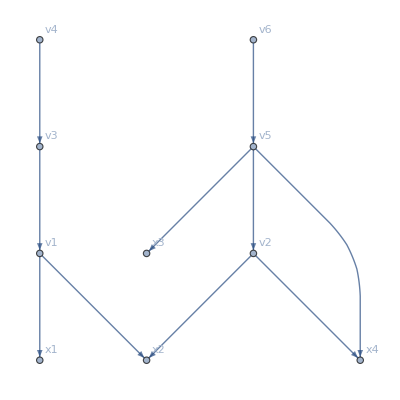
FindPath[-Graphics-,v6,{x1,x2,x3,x4},∞,All]

```mathematica
FindPath[$graph, "v6", xVar[[All, 1]], Infinity, All]
```

```mathematica
FindPath[$graph, "v6",#, Infinity, All] & /@ xVar[[All, 1]]
```

{{},{{v6,v5,v2,x2}},{{v6,v5,x3}},{{v6,v5,x4},{v6,v5,v2,x4}}}

```mathematica
DeleteCases[FindPath[$graph, "v6",#, Infinity, All] & /@ xVar[[All, 1]], {}]
```

{{{v6,v5,v2,x2}},{{v6,v5,x3}},{{v6,v5,x4},{v6,v5,v2,x4}}}

```mathematica
calcSensitivityOnePath[$tape,{"v6","v5","x4"} ]
```

tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]

```mathematica
calcSensitivityOnePath[$tape,{"v6","v5","v2","x4"} ]
```

tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(0,1)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4]

```mathematica
calcSensitivityOneVariable[$tape, {{"v6","v5","x4"},{"v6","v5","v2","x4"}}]
```

<|x4→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]+tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(0,1)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4]|>

```mathematica
calcSensitivityOneVariable[$tape, {{"v6","v5","x3"}}]
```

<|x3→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4]|>

```mathematica
Join[calcSensitivityOneVariable[$tape, {{"v6","v5","x4"},{"v6","v5","v2","x4"}}], calcSensitivityOneVariable[$tape, {{"v6","v5","x3"}}]]
```

<|x4→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]+tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(0,1)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4]|>

```mathematica
calcSensitivity[$graph, $tape, xVar, "v6"]
```

<|x2→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(1,0)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4],x3→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,1,0)[wfun[x2,x4],x3,x4],x4→tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] yfun[wfun[x2,x4],x3,x4]^(0,0,1)[wfun[x2,x4],x3,x4]+tfun[yfun[wfun[x2,x4],x3,x4]]'[yfun[wfun[x2,x4],x3,x4]] wfun[x2,x4]^(0,1)[x2,x4] yfun[wfun[x2,x4],x3,x4]^(1,0,0)[wfun[x2,x4],x3,x4]|>

```mathematica
calcSensitivity[$graph, $tape, xVar, "v4"]
```

<|x1→vfun[ufun[x1,x2]]'[ufun[x1,x2]] zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]] ufun^(1,0)[x1,x2],x2→vfun[ufun[x1,x2]]'[ufun[x1,x2]] zfun[vfun[ufun[x1,x2]]]'[vfun[ufun[x1,x2]]] ufun^(0,1)[x1,x2]|>